#### WOLFRAM MATERIALS for the ARTICLE:

S. Hamis, P. Somervuo, J.A. Ågren, D.S. Tadele, J. Kesseli, J. Scott, M. Nykter, P. Gerlee, D. Finkelshtein, O. Ovaskainen (2022). 
Spatial cumulant models enable spatially informed treatment strategies and analysis of local interactions in cancer systems.
bioRxiv, Cold Spring Harbor Laboratory Preprints. 
doi and article link: https://doi.org/10.1101/2022.05.07.491050. 
The full code project is available here: https://github.com/SJHamis/SpatialCumulantModels_CancerApplications.

## Abstract

Cancer studies that use individual-based models (IBMs) have been limited by the lack of a mathematical formulation that enables rigorous analysis of these models. However, spatial cumulant models (SCMs), which have arisen from recent advances in Theoretical Ecology, are analytical models that describe population dynamics generated by a specific family of IBMs, namely spatio-temporal point processes (STPPs).

Here, we exemplify how SCMs can be used in mathematical oncology by modelling a theoretical cancer cell population comprising both growth factor producing and non-producing cells. Our results demonstrate (1) that SCMs can capture STPP-generated population density dynamics, even when mean-field population models (MFPMs) fail to do so, and (2) that SCM-informed treatment strategies outperform MFPM-informed strategies in terms of inhibiting population growths.

We argue that SCMs provide a new framework in which to study cell-cell interactions, and can be used to deepen the mathematical analysis of IBMs and thereby increase IBMs’ applicability in cancer research.

## 1. Introduction

SCMs are spatially resolved population models formulated by a system of ordinary differential equations that approximate the dynamics of two STPP-generated summary statistics: first order spatial cumulants (densities u^(1)), and second order spatial cumulants (spatial covariances u^(2)). Following a mathematical manipulation that involves a perturbation expansion around the mean-field equations in the limit of long-ranged interactions (Ovaskainen et al. 2014), SCMs can be expressed as:



The independent variables t and r respectively denote time and pair-wise distances between individuals (in our case cells).  d denotes the dimension of the modelled spatial domain and ϵ=1/L is a scaling parameter, where L denotes a typical interaction length scale. Note that when L→∞, the SCM density equation reduces to the mean-field equation.  The terms o(ϵ^d) can be omitted in practical applications.

Deriving the expressions for q, p, and g , for some biological system of interest, is generally a mathematically cumbersome task. However, Cornell et al. (2019) developed a Wolfram Mathematica Library Package that automates the generation of q, p and g for any biological system that can be expressed by one or more reactant-catalyst-product (RCP) processes. In such RCP-processes,

• reactants are individuals (here cells) that are are consumed in the process,
• catalysts catalyse the process (without getting consumed in it),
• products are produced in the process. 

Cell division can, for example, be described by one catalyst (the mother cell) and one product (the daughter cell). 

In STPPs and SCMs, the rate (probability per time unit) that two individuals (cells) interact with each other is described by interaction kernels that are functions of pair-wise distances between cells. In the figure below, for example, the focal red cell is more likely to interact with nearby green cells than with faraway green cells (a). In MFPMs, on the other hand, any focal cell is equally likely to interact with all other cells in the system (b). 

-Graphics-

## 2. Model

We model a cancer system that consists of two cell subpopulations: growth factor producer-cells (subpopulation s_1, red) and non-producer-cells (subpoulation s_(2,) green). 

-Graphics-

The cells need growth factors in order to divide. As illustrated in the above figure, producer-cells can internalise growth factors produced by themselves (a) or by other producer-cells (b). Non-producer-cells must receive growth factors from producer-cells in order to divide (c). The size of the plus-sign indicates the benefit, in terms of proliferation rate, that a cell gains from a depicted cell-cell interaction. Note that it is beneficial for cells to “free-load” on external growth factors, because then they do not need to spend energy on growth-factor production. Additionally, if drugs are applied to the system, the cells may die. 

This cancer system can be compactly described by five reactant-catalyst-product (RCP) processes: 

Biological process | Reactants (r),
catalysts (c),
products (p). | Description
Birth[s_1,B_1(x_1-x_2)] | r=⌀,
c={x_(1,)s_1},
p={x_(2,)s_1}. | A cell with mark s_1 in location x_1 produces a cell
of mark s_1 in location x_2 with kernel B_1(x_1-x_2). 
See (a)in the figure above.
Birth By Facilitation
[s_1,s_1,B_11(x_1-x_2),C(x_1-x_3)] | r=⌀,
c={{x_(1,)s_1},{x_(3,)s_1}},
p={x_(2,)s_1}. | A cell with mark s_1 in location x_1 produces a cell 
of mark s_1 in location x_2 with kernel B_11(x_1-x_2).
This process is facilitated by a cell with mark s_1
in location x_3 with kernel C(x_1-x_2).
See (b)in the figure above.
Birth By Facilitation
[s_2,s_1,B_12(x_1-x_2),C(x_1-x_3)] | r=⌀,
c={{x_(1,)s_2},{x_(3,)s_1}},
p={x_(2,)s_2}. | A cell with mark s_2 in location x_1 produces a cell 
of mark s_2 in location x_2 with kernel B_11(x_1-x_2).
This process is facilitated by a cell with mark s_1
in location x_3 with kernel C(x_1-x_2). 
See (c)in the figure above.
Density Independent Death[s_1,δ_1] | r={x_(1,)s_1},
c=⌀,
p=⌀. | A cell with mark s_1 in location x_1 dies at rate δ_1.
Density Independent Death[s_2,δ_2] | r={x_(1,)s_2},
c=⌀,
p=⌀. | A cell with mark s_2 in location x_1 dies at rate δ_2.

We are going to investigate s_1 and s_2 density dynamics resulting from three different initial cell configurations (ICCs). These are shown in the left-most column in the figure below. Note that the number of s_1 and s_2 cells are the same in ICCs 1, 2 and 3. For each investigated ICC, snapshots from one STPP-generated cell population is shown at time points 0, 100 and 200 Δt below.
 -Graphics-

Since the cell-cell interactions are localised in space via interaction kernels, STPP-generated density dynamics depend on the spatial structure of the cell populations. As such, the density dynamics resulting from ICCs 1, 2 and 3 are notably different. On the other hand, MFPM-generated density dynamics resulting from ICCs 1, 2 and 3 all will be the same (since MFPMs are not spatially resolved).

## 3. Implementation

#### 3.1 Import Wolfram Mathematica Libraries

To formulate SCMs, we import the following libraries developed by Cornell et al. (2019):

```mathematica
Get["SSPPlibraryOfProcesses`"]
```

```mathematica
Get["SSPPanalyticalExpressions`"]
```

These libraries can be downloaded from https://doi.org/10.6084/m9.figshare.9633161.

#### 3.2 Define the reactant-catalyst-product processes for the modelled system

We then define the modelled system in terms of the RCP-processes that are tabulated in the Model description. 
Note: To see a list of all pre-defined RCP-processes included in the imported libraries, use the command: ?SSPPlibraryOfProcesses`*

```mathematica
rcpProcesses={
Birth[1,b1,B1,1],
BirthByFacilitation[1,1,h,H,b11,B11,1],
BirthByFacilitation[2,1,h,H,b12,B12,1],
DensityIndependentDeath[1,d1,1],
DensityIndependentDeath[2,d2,1]};
```

#### 3.3 Define variable names and helpful substitutions

We define variable names and substitutions that will simplify both analytical and numerical calculations further down in the Notebook:

```mathematica
qpgVariables={q,p,g};
kVariableInG=k;
variableOfIntegrationFT=k;
xVariableInG=x;
variableOfIntegration=x;
dim=2;
```

```mathematica
listOfNumericalSubs={q[1]-> q1[t], q[2]-> q2[t],p[1]-> p1[t], p[2]-> p2[t],
g[1,1,k]->G11[t,k],g[1,2,k]->G12[t,k],g[2,2,k]->G22[t,k],
B1[0] -> totIntB1,B11[0] -> totIntB11,B12[0] -> totIntB12,H[0] -> totIntH
 };
```

```mathematica
listOfWSubs={2 π ∫_0^∞ k totIntB11 G11[t,k] H[k]ⅆk-> W11[t],2 π ∫_0^∞ k totIntB12 G12[t,k] H[k]ⅆk-> W12[t] };
```

```mathematica
listOfAnalyticalSubs={q1[t]->q1,q2[t]->q2,p1[t]->p1,p2[t]->p2,d-> 2,W11[t]->W11,W12[t]->W12 };
```

Above, we have introduced the functions W11 and W12 in order to (further down) separate terms that will be numerically calculated in real space, from those that will be calculated in Fourier space.

#### 3.4 Generate equations that describe density and spatial covariance dynamics

We generate rate equations for q, p and g using the functions HQfALL, HPfALL and HGfALL respectively. 
Note: To see function syntax, use the command: ?SSPPanalyticalExpressions`*

We label the right-hand-sides of the rate equations as follows:

dq_1/dt =Hq1, dq_2/dt =Hq2, 
dPp_1/dt =Hp1, dp_2/dt =Hp2,  
dg_11/dt =Hg11, dg_12/dt =Hg12, dg_22/dt =Hg22,

where the subscripts 1 and 2 correspond so subpopulations s_1 and s_2, respectively.

```mathematica
Hq1=HQfALL[qpgVariables,rcpProcesses,1]//.listOfNumericalSubs
```

-d1 q1[t]+totIntB1 q1[t]+totIntB11 totIntH q1[t]^2

```mathematica
Hq2=HQfALL[qpgVariables,rcpProcesses,2]//.listOfNumericalSubs
```

-d2 q2[t]+totIntB12 totIntH q1[t] q2[t]

```mathematica
Hp1=HPfALL[qpgVariables,rcpProcesses,1,variableOfIntegrationFT,dim]//.listOfNumericalSubs //.listOfWSubs
```

-d1 p1[t]+totIntB1 p1[t]+2 totIntB11 totIntH p1[t] q1[t]+W11[t]

```mathematica
Hp2=HPfALL[qpgVariables,rcpProcesses,2,variableOfIntegrationFT,dim]//.listOfNumericalSubs  //.listOfWSubs
```

-d2 p2[t]+totIntB12 totIntH (p2[t] q1[t]+p1[t] q2[t])+W12[t]

```mathematica
HG11=HGfALL[qpgVariables,rcpProcesses,1,1,kVariableInG]//.listOfNumericalSubs
```

-2 d1 G11[t,k]+2 B1[k] G11[t,k]+2 B1[k] q1[t]+2 totIntH B11[k] G11[t,k] q1[t]+2 B11[k] G11[t,k] H[k] q1[t]+(2 totIntH B11[k]+2 B11[k] H[k]) q1[t]^2

```mathematica
HG12=HGfALL[qpgVariables,rcpProcesses,1,2,kVariableInG]//.listOfNumericalSubs
```

-d1 G12[t,k]-d2 G12[t,k]+B1[k] G12[t,k]+totIntH B11[k] G12[t,k] q1[t]+totIntH B12[k] G12[t,k] q1[t]+B11[k] G12[t,k] H[k] q1[t]+B12[k] G11[t,k] H[k] q2[t]+B12[k] H[k] q1[t] q2[t]

```mathematica
HG22=HGfALL[qpgVariables,rcpProcesses,2,2,kVariableInG]//.listOfNumericalSubs
```

-2 d2 G22[t,k]+2 totIntH B12[k] G22[t,k] q1[t]+2 B12[k] G12[t,k] H[k] q2[t]+2 totIntH B12[k] q1[t] q2[t]

Here, G is the Fourier-transform of g, and k is the independent variable in Fourier space.

#### 3.5 Find the death rates that stop the subpopulation densities from increasing

Next, we derive both MFPM-informed and SCM-informed “drug doses” (implicitly modelled via the death rates d1 and d2) that stop the subpopulations from growing. In other words, we find the values d1 and d2 such that the density rate equations equal zero. Accordingly, 
• MFPM-informed death rates are obtained by: Hq1:=0 and Hq2:=0,
• SCM-informed death rates are obtained by: Hq1+ϵ^dHp1:=0 and Hq2+ϵ^dHp2:=0.

To solve for d1 and d2, we first define model parameter assumptions that simplify the calculations:

```mathematica
modelAssumptions= {
totIntB1∈Reals,totIntB11∈Reals,totIntB12∈Reals,totIntH∈Reals,d1∈Reals,d2∈Reals,
q1∈Reals,q2∈Reals,p1 ∈Reals, p2∈Reals,W11∈Reals,W12∈Reals,ϵ∈Reals,
totIntB1≥ 0, totIntB11≥ 0, totIntB12≥0,totIntH≥ 0,d1≥0,d2≥0,q1≥0,q2≥0,ϵ≥0};
```

We then solve for the MFMP-informed death rates:

```mathematica
eqsMF= {Hq1==0, Hq2==0} //.listOfAnalyticalSubs;
solsMF =Simplify[Solve[eqsMF,{d1,d2}],modelAssumptions]
```

{{d1→totIntB1+q1 totIntB11 totIntH,d2→q1 totIntB12 totIntH}}

And we solve for the SCM-informed death rates:

```mathematica
eqsSCM = {Hq1 +ϵ^d* Hp1==0,Hq2 +ϵ^d* Hp2==0} //.listOfAnalyticalSubs;
solsSCM=Simplify[Solve[eqsSCM,{d1,d2}],modelAssumptions]/. {p1-> 0,p2-> 0}
```

{{d1→(q1 totIntB1+q1^2 totIntB11 totIntH+W11 ϵ^2)/q1,d2→q1 totIntB12 totIntH+(W12 ϵ^2)/q2}}

In the full code project associated with our research article, these death rates are applied to STPPs at the treatment time T (in a C code). For each STPP-generated cancer cell population, we thus measure the quantities q1(T), q2(T), W11(T) and W12(T). By setting the correction densities p1(T) and p2(T) to zero, and working with known model constants, we can thus calculate numerical values for d1(T) and d2(T). We do this for both MFPM and SCM informed death rates.

#### 3.6 Assign numerical model parameter values

We now assign numerical values to the constant model parameters. We use Gaussian interaction kernels, with integrals and standard deviations labeled with prefixes “totInt” and “σ” respectively.

The model parameters pertaining to cell division are:

```mathematica
celldivparams = {totIntB1->0.001,totIntB11->0.025,totIntB12->0.05,σB1->25,σB11->25,σB12->25};
kernelB1 = {B1->   (totIntB1 Exp[-2 π^2  (#)^2 σB1^2] &) }/.celldivparams;
kernelB11 ={B11 -> (totIntB11 Exp[-2 π^2 (#)^2 σB11^2] &) }/.celldivparams;
kernelB12 ={B12 -> (totIntB12 Exp[-2 π^2 (#)^2 σB12^2] &) }/.celldivparams;
```

And the model parameters pertaining to cell-cell communication via growth factors are:

```mathematica
comparams = {totIntH ->100,σH->100};
kernelH ={H-> ( totIntH Exp[-2  π^2  (#)^2 σH^2] &) }/.comparams;
```

For simplicity, we gather all kernel rules:

```mathematica
kernelrules = Flatten[{celldivparams,kernelB1,kernelB11,kernelB12,comparams,kernelH}];
```

Before drugs are applied to the system, the model parameters pertaining to cell death are:

```mathematica
noDrugDeathRates = {d1-> 0,d2->0};
```

Lastly, we define the model parameters that pertain to scaling and STPP sampling:

```mathematica
L=1.;
epsilonrule ={ϵ->SetPrecision[1/L,40]};
tmin =0;
tmax=200;
qside=1000;
rmin = 0;
rmax=qside/2;
rbin = 10;
kmin = 10^-20;
kmax =0.02;
```

Here, tmin and tmax denote the start and end time of the simulation. The modelled spatial domain is a square with side qside. Minimum and maximum cell-cell separation values are given by rmin and rmax, where rmax=qside/2, as we are using periodic boundary conditions. Cell-cell separations are, moreover, sampled from STPPs with a spatial bin-size rbin. kmin and kmax denote the minimum and maximum value of the independent variable in Fourier space.

#### 3.7 Choose the initial cell configuration

We choose the ICC that we wish to use. The possible options are 1, 2 or 3 (see the last figure in Notebook Section 2) :

```mathematica
ICCoption = 2;
```

#### 3.8 Import STPP density and spatial covariance data

STPP dynamics resulting from the three regarded ICCs are simulated in a C-based code. In this Notebook, data describing such STPP dynamics are simply imported from files.

Note that the STPP is stochastic and can, for a given ICC, generate an ensemble of different spatio-temporal point patterns (cell configurations). We therefore import the minimum, mean and maximum density data from 100 STPP simulations per ICC.  These files describe the density dynamics when no when no drugs/cell deaths are applied to the system:

```mathematica
datafilelocation=StringJoin[NotebookDirectory[],"DataFromSTPPs/DensityDataNoCellDeath/ICC",ToString[ICCoption]];
mindensity1STPP=Import[StringJoin[datafilelocation,"/u1_subpop1_mindensity.csv"]];
meandensity1STPP=Import[StringJoin[datafilelocation,"/u1_subpop1_meandensity.csv"]];
maxdensity1STPP=Import[StringJoin[datafilelocation,"/u1_subpop1_maxdensity.csv"]];
mindensity2STPP=Import[StringJoin[datafilelocation,"/u1_subpop2_mindensity.csv"]];
meandensity2STPP=Import[StringJoin[datafilelocation,"/u1_subpop2_meandensity.csv"]];
maxdensity2STPP=Import[StringJoin[datafilelocation,"/u1_subpop2_maxdensity.csv"]];
```

In preparation for plotting, we then interpolate the minimum and maximum density data:

```mathematica
mindensity1STPPip=Interpolation[mindensity1STPP,InterpolationOrder->1];
maxdensity1STPPip=Interpolation[maxdensity1STPP,InterpolationOrder->1];
mindensity2STPPip=Interpolation[mindensity2STPP,InterpolationOrder->1];
maxdensity2STPPip=Interpolation[maxdensity2STPP,InterpolationOrder->1];
```

We next import the spatial covariance data for the investigated ICC:

```mathematica
datafilelocation=StringJoin[NotebookDirectory[],"DataFromSTPPs/SpatialCovarianceData/ICC",ToString[ICCoption]];
spatcov11STPPtime0=Import[StringJoin[datafilelocation,"/u2_subpops11_time0.csv"]];
spatcov12STPPtime0=Import[StringJoin[datafilelocation,"/u2_subpops12_time0.csv"]];
spatcov22STPPtime0=Import[StringJoin[datafilelocation,"/u2_subpops22_time0.csv"]];
```

#### 3.9 Set the SCM and MFPM initial conditions from the imported STPP data

The initial conditions for q (densities) and g (spatial covariances) are set from the imported data. The initial correction values p1(0) and p2(0) are set to zero. Note that the initial conditions g(t,r) must be Fourier-transformed (or, more specifically, Hankel-transformed in our case with d=2 and radial symmetry) to form G(t,k), in accordance with the generated SCM equations.

```mathematica
defaultICq = {ICq1->meandensity1STPP[[1,2]], ICq2->meandensity2STPP[[1,2]]};
defaultICp = {ICp1->0, ICp2->0};
HankelTransformu2[k_,u2profile_]:=Sum[u2profile[[i]] ((i (rbin*ϵ)) BesselJ[1,2 i (rbin*ϵ) Pi k]/k-((i-1) (rbin*ϵ)) BesselJ[1,2 (i-1) (rbin*ϵ) Pi k]/k /.epsilonrule),{i,1,Length[u2profile]}];
defaultICG = {
ICG11->HankelTransformu2[k,spatcov11STPPtime0[[All,2]]],
ICG12->HankelTransformu2[k,spatcov12STPPtime0[[All,2]]],
ICG22->HankelTransformu2[k,spatcov22STPPtime0[[All,2]]]
};
defaultICs=Union[defaultICq, defaultICp,defaultICG];
```

#### 3.10 Solve the SCM and MFPM equations numerically

In preparation for the numerical calculations, we define the model rate equations using the previously obtained expressions for Hq1, Hq2, Hp1, Hp2, HG11, HG12, HG22 and the initial conditions:

```mathematica
eqq1 ={D[q1[t],t]==Hq1,q1[0]==ICq1} /. kernelrules;
eqq2 ={D[q2[t],t]==Hq2,q2[0]==ICq2} /. kernelrules;
eqp1 ={D[p1[t],t]== Hp1,p1[0]==ICp1} /. kernelrules;
eqp2 ={D[p2[t],t]==Hp2,p2[0]==ICp2} /. kernelrules;
eqG11={D[G11[t,k],t]==HG11,G11[0,k]==ICG11} /. kernelrules;
eqG12={D[G12[t,k],t]==HG12,G12[0,k]==ICG12} /. kernelrules ;
eqG22={D[G22[t,k],t]==HG22,G22[0,k]==ICG22} /. kernelrules;
```

We are now ready to define a function that numerically calculates q, p and g (or rather, G):

```mathematica
SolveModelEquations[deathrule0_, ICsrule0_]:= Module[{deathrule=deathrule0, ICsrule=ICsrule0},
procedeqq1 = eqq1 /.deathrule /.ICsrule;
procedeqq2 = eqq2 /.deathrule /.ICsrule;
procedeqp1 = eqp1 /.deathrule /.ICsrule;
procedeqp2 = eqp2 /.deathrule /.ICsrule;
procedeqG11 = eqG11 /.deathrule /.ICsrule;
procedeqG12 = eqG12 /.deathrule /.ICsrule;
procedeqG22 = eqG22 /.deathrule /.ICsrule;
qsols=Flatten[NDSolve[Flatten[{procedeqq1,procedeqq2}],{q1,q2},{t,0,tmax}]];
geqs =Union[procedeqG11,procedeqG12, procedeqG22]/.qsols;
maxcellmeasure = 0.0001;
gsols =
NDSolve[geqs,{G11,G12,G22},{t,tmin,tmax},{k,kmin,kmax}, AccuracyGoal->10, PrecisionGoal->20, Method->"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","MeshOptions"->{"MaxCellMeasure"->maxcellmeasure}}}] //Flatten;
W11[t_?NumericQ]:=2π NIntegrate[k*totIntB11*( G11[t,k]/.gsols)*(H[k]) /.kernelrules, {k,kmin,kmax},WorkingPrecision->10,PrecisionGoal->3] ;
W12[t_?NumericQ]:=2π NIntegrate[k*totIntB12*( G12[t,k]/.gsols)*(H[k]) /.kernelrules, {k,kmin,kmax},WorkingPrecision->10,PrecisionGoal->3] ;
peqs=Union[SetPrecision[procedeqp1,40],SetPrecision[procedeqp2,40]] /.qsols /.gsols;
psols = Flatten[NDSolve[peqs,{p1,p2}, {t,0,tmax},WorkingPrecision->10]];
{qsols, gsols, W11, W12,psols}
]
```

And with the following command, we can now obtain q, p and G:

```mathematica
solsdefault=SolveModelEquations[noDrugDeathRates, defaultICs];
```

## 4. Visualise Results

We visualise density dynamics generated by the STPP, MFPM and SCM in three different plots (4.1-4.3). To allow for visual comparison, we then overlay the plots in 4.4.

#### 4.1 Generate the STPP density dynamics plot (pre-drug)

```mathematica
plotSTPPdensity=Plot[{mindensity1STPPip[t],mindensity2STPPip[t],maxdensity1STPPip[t],maxdensity2STPPip[t]},{t,0,tmax},
PlotStyle->{RGBColor[1,0,0,0.2],RGBColor[0,1,0.5,0.2],RGBColor[1,0,0,0.2],RGBColor[0,1,0.5,0.2]},
Filling->{ {1->{{3},RGBColor[1,0,0,0.2]}} ,{2->{{4},RGBColor[0,1,0.5,0.2]}} },FillingStyle->Automatic,
PlotLegends->Placed[{ "s_1 min-to-max (SPP)","s_2 min-to-max (SPP)",None,None},Right],
AxesLabel->{"t", "(u^(1))_i(t)"},PlotRange->Full,PlotLabel->StringForm["Density dynamics."] ];
```

#### 4.2 Generate the MFPM density dynamic plots (pre-drug)

```mathematica
plotMFPMdensity = Plot[{(q1[t]/. qsols), q2[t]/. qsols},{t,0,tmax},
PlotStyle->{{RGBColor[0.81,0.,0.19],Thick},{RGBColor[0.4,0.5,0.],Thick}},
PlotRange->{{0,200},{0.00024,0.0004}},AxesLabel->{"t", "(u^(1))_i(t)"},
PlotLegends->Placed[{ "s_1(MFPM)","s_2 (MFPM)",None,None},Right]];
```

#### 4.3 Generate the SCM density dynamic plots (pre-drug)

```mathematica
SCMMarkersSubpop1= Table[{t,(q1[t] /. qsols)+ ϵ^2(p1[t]/.psols) /.epsilonrule},{t,10,200,10}];
SCMMarkersSubpop2 =Table[{t,(q2[t] /. qsols)+ ϵ^2(p2[t]/.psols) /.epsilonrule},{t,10,200,10}];
plotSCMdensity=ListPlot[{SCMMarkersSubpop1,SCMMarkersSubpop2},PlotMarkers->{{"▲",Small},{"▲",Small}},
PlotStyle->{RGBColor[0.81,0.,0.19],RGBColor[0.4,0.5,0.]},
PlotLegends->Placed[{ "s_1(SCM)","s_2 (SCM)",None,None},Right]];
```

#### 4.4. Overlay the density dynamic plots for visual model comparisons (pre-drug)

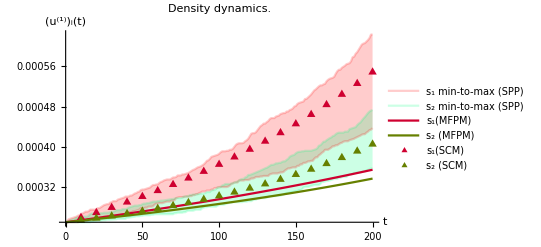

```mathematica
ComparisonPlot=Show[plotSTPPdensity,plotMFPMdensity,plotSCMdensity]
```

#### 4.5 Results presented in the original research article

In the original research article, we show that SCMs can capture STPP-generated population density dynamics, even when mean-field population models (MFPMs) fail to do so. As can be seen in the figure below, for ICC.1, both the MFPM and the SCM capture STPP density dynamics. However, for ICCs 2 and 3, the SCM captures STPP density dynamics whereas the MFPM does not. 
You can verify this by changing the variable “ICCoption” in 3.7! 
-Graphics-

We also show that SCM-informed treatment strategies outperform MFPM-informed strategies in terms of inhibiting population growths. Following the procedure outlined in 3.5, drugs are applied at time T=200Δt in the STPP. The resulting density dynamics are shown in the figure below, in which each track corresponds to one spatio-temporal point pattern (STPP-generated cancer cell population). 

-Graphics-

## 5. Significance and Concluding Remarks

Due to the pre-clinical and clinical applications of mathematical oncology models (Rockne et al., 2019), there exists a need to formulate analytical cancer models that capture localised cell-cell interactions, maintain cell discreteness and are spatio-temporal. In this work, we suggested using spatial cumulant models (SCMs) to achieve this. 

Deriving SCMs for a specific biological system can be a mathematically challenging and cumbersome task. However, using a Wolfram Mathematica Library Package, the generation of SCMs can be automated for a broad family of biological systems (more specifically any system that can be described in terms of reactant-catalyst-product processes). 

In this Notebook, we used Wolfram Mathematica to
(1) generate SCMs and MFPMs that describe our regarded cancer system, 
(2) analytically derive spatially informed treatment strategies via SCMs (and non-spatially informed treatment strategies via MFPMs),
(3) numerically solve the SCM and MFPM equations, 
(4) visually compare the resulting STPP, SCM and MFPM density dynamics. 

We anticipate that the opportunity to analytically derive spatially informed cancer treatment strategies, as enabled via SCMs, will inspire new theoretical and applied research ventures.

## References

S. J. Cornell, Y. F. Suprunenko, D. Finkelshtein, P. Somervuo, and O. Ovaskainen. A unified framework for analysis of individual-based models in ecology and beyond. Nat Commun, 10(1):4716, 10 2019. doi: https://doi.org/10.1038/s41467-019-12172-y.

O. Ovaskainen, D. Finkelshtein, O. Kutoviy, S. Cornell, B. Bolker, and Y. Kondratiev. A general mathematical framework for the analysis of spatiotemporal point processes. Theor Ecol, 7:101–113, 2014. doi: https://doi.org/10.1007/s12080-013-0202-8.

R. C. Rockne, A. Hawkins-Daarud, K. R. Swanson, J. P. Sluka, J. A. Glazier, P. Macklin, D. A. Hor- muth, A. M. Jarrett, E. A. B. F. Lima, J. Tinsley Oden, G. Biros, T. E. Yankeelov, K. Curtius, I. Al Bakir, D. Wodarz, N. Komarova, L. Aparicio, M. Bordyuh, R. Rabadan, S. D. Finley, H. En- derling, J. Caudell, E. G. Moros, A. R. A. Anderson, R. A. Gatenby, A. Kaznatcheev, P. Jeavons, N. Krishnan, J. Pelesko, R. R. Wadhwa, N. Yoon, D. Nichol, A. Marusyk, M. Hinczewski, and J. G. Scott. The 2019 mathematical oncology roadmap. Phys Biol, 16(4):041005, 06 2019. doi: https://doi.org/10.1088/1478-3975/ab1a09.